```mathematica
:=
```

```mathematica
!
```

```mathematica
4!
```

24

```mathematica
5=!=5
```

False

```mathematica
?/.
```

```mathematica
10/.{10->5}
```

5

```mathematica
/;
```

```mathematica
_?
```

```mathematica
Clear[a,b,c]
{a,b,c}/.a->Sequence[]
```

{b,c}

## Condition Function

```mathematica
f[x_?x==10]:=x^2
```

```mathematica
g[x_]/;x==10:=x^2
```

```mathematica
f[2]
```

f[2]

```mathematica
f[10]
```

100

```mathematica
g[3]
```

g[3]

```mathematica
g[10]
```

100

```mathematica
myList=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
ReplacePart[myList,4->100]
```

{1,2,3,100,5,6,7,8,9,10}

```mathematica
myList[[2]]=2000
```

2000

```mathematica
myList
```

{1,2000,3,4,5,6,7,8,9,10}

```mathematica
myList=ReplacePart[myList,4->100]
```

{1,2000,3,100,5,6,7,8,9,10}

```mathematica
Position[myList,2000]
```

{{2}}

### 重要条件

```mathematica
{a,b,"c",32,324.4,23,d}/._Integer->"I am an integer"
```

{a,b,c,I am an integer,324.4,I am an integer,d}

```mathematica
{a,b,"c",32,324.4,23,d}/.a_Integer->1000*a
```

{a,b,c,32000,324.4,23000,d}

```mathematica
{a,b,"c",32,324.4,23,d}/.{a_Integer->1000*a,a_Real->10*a,a_?StringQ->"i am a string"}
```

{a,b,i am a string,32000,3244.,23000,d}

```mathematica
{a,b,"c",32,324.4,23,d}/.a_?EvenQ->1000*a
```

{a,b,c,32000,324.4,23,d}

```mathematica
{a,b,c}/.(x_/;AtomQ[x]):>RandomReal[]*x
```

(0.0647619 List)[0.706571 a,0.032678 b,0.816758 c]

## 分配率

```mathematica
f/@Range[5]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Cos/@Range[5]
```

{Cos[1],Cos[2],Cos[3],Cos[4],Cos[5]}

```mathematica
N[Cos[1]]
```

0.540302

```mathematica
N[Cos/@Range[5]]
```

{0.540302,-0.416147,-0.989992,-0.653644,0.283662}

```mathematica
Cos[#]&/@Range[5]
```

{Cos[1],Cos[2],Cos[3],Cos[4],Cos[5]}

```mathematica
complexList= Range[5*#,5*#+4]&/@Range[5]
```

{{5,6,7,8,9},{10,11,12,13,14},{15,16,17,18,19},{20,21,22,23,24},{25,26,27,28,29}}

```mathematica
Range[5*#,5*#+4]/.#->Range[5]
```

{{5,10,15,20,25},{6,11,16,21,26},{7,12,17,22,27},{8,13,18,23,28},{9,14,19,24,29}}

```mathematica
complexList//MatrixForm
```

(5 | 6 | 7 | 8 | 9
10 | 11 | 12 | 13 | 14
15 | 16 | 17 | 18 | 19
20 | 21 | 22 | 23 | 24
25 | 26 | 27 | 28 | 29)

```mathematica
Last[complexList]
```

{25,26,27,28,29}

```mathematica
Map[Last,complexList]
```

{9,14,19,24,29}

```mathematica
Map[Extract[#,4]&,complexList]
```

{8,13,18,23,28}

```mathematica
Map[#[[4]]&,complexList]
```

{8,13,18,23,28}

```mathematica
#[[4]]&/@complexList
```

{8,13,18,23,28}

```mathematica
Table[complexList[[i,i]],{i,1,5}]
```

{5,11,17,23,29}

```mathematica
Table[{i,j},{i,1,5},{j,1,4}]//MatrixForm
```

((1
1) | (1
2) | (1
3) | (1
4)
(2
1) | (2
2) | (2
3) | (2
4)
(3
1) | (3
2) | (3
3) | (3
4)
(4
1) | (4
2) | (4
3) | (4
4)
(5
1) | (5
2) | (5
3) | (5
4))

```mathematica
Table[i*j,{i,1,5},{j,1,4}]//MatrixForm
```

(1 | 2 | 3 | 4
2 | 4 | 6 | 8
3 | 6 | 9 | 12
4 | 8 | 12 | 16
5 | 10 | 15 | 20)

```mathematica
(myMatrix=Table[complexList[[i,j]],{i,1,5},{j,1,4}])//MatrixForm
```

(5 | 6 | 7 | 8
10 | 11 | 12 | 13
15 | 16 | 17 | 18
20 | 21 | 22 | 23
25 | 26 | 27 | 28)

```mathematica
Table[myMatrix[[i,i]],{i,1,4}]
```

{5,11,17,23}

```mathematica
(myNewMatrix=Table[{i,j},{i,1,6},{j,1,4},{k,1,2}])//MatrixForm
```

((1 | 1
1 | 1) | (1 | 2
1 | 2) | (1 | 3
1 | 3) | (1 | 4
1 | 4)
(2 | 1
2 | 1) | (2 | 2
2 | 2) | (2 | 3
2 | 3) | (2 | 4
2 | 4)
(3 | 1
3 | 1) | (3 | 2
3 | 2) | (3 | 3
3 | 3) | (3 | 4
3 | 4)
(4 | 1
4 | 1) | (4 | 2
4 | 2) | (4 | 3
4 | 3) | (4 | 4
4 | 4)
(5 | 1
5 | 1) | (5 | 2
5 | 2) | (5 | 3
5 | 3) | (5 | 4
5 | 4)
(6 | 1
6 | 1) | (6 | 2
6 | 2) | (6 | 3
6 | 3) | (6 | 4
6 | 4))

```mathematica
Table[myNewMatrix[[i]][[j]][[k]],{i,1,4},{j,1,4},{k,1,2}]//MatrixForm
```

((1 | 1
1 | 1) | (1 | 2
1 | 2) | (1 | 3
1 | 3) | (1 | 4
1 | 4)
(2 | 1
2 | 1) | (2 | 2
2 | 2) | (2 | 3
2 | 3) | (2 | 4
2 | 4)
(3 | 1
3 | 1) | (3 | 2
3 | 2) | (3 | 3
3 | 3) | (3 | 4
3 | 4)
(4 | 1
4 | 1) | (4 | 2
4 | 2) | (4 | 3
4 | 3) | (4 | 4
4 | 4))

```mathematica
Table[myNewMatrix[[i,i,2,1]],{i,1,4}]
```

{1,2,3,4}

```mathematica
(myNewMatrix1=Table[i*j,{i,1,6},{j,1,4},{m,1,2},{n,2,3}])//MatrixForm
```

((1 | 1
1 | 1) | (2 | 2
2 | 2) | (3 | 3
3 | 3) | (4 | 4
4 | 4)
(2 | 2
2 | 2) | (4 | 4
4 | 4) | (6 | 6
6 | 6) | (8 | 8
8 | 8)
(3 | 3
3 | 3) | (6 | 6
6 | 6) | (9 | 9
9 | 9) | (12 | 12
12 | 12)
(4 | 4
4 | 4) | (8 | 8
8 | 8) | (12 | 12
12 | 12) | (16 | 16
16 | 16)
(5 | 5
5 | 5) | (10 | 10
10 | 10) | (15 | 15
15 | 15) | (20 | 20
20 | 20)
(6 | 6
6 | 6) | (12 | 12
12 | 12) | (18 | 18
18 | 18) | (24 | 24
24 | 24))

```mathematica
Table[myNewMatrix2[[i,i,2,1]]=100*myNewMatrix1[[I,I,2,1]],{I,1,4}]
```

Set::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Set::pkspec1 will be suppressed during this calculation.

{100,400,900,1600}

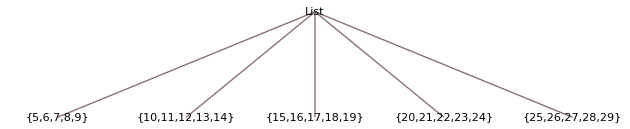

```mathematica
complexList//TreeForm
```

```mathematica
Position[complexList,27|13]
```

{{2,4},{5,3}}

```mathematica
Extract[complexList,{2,4}]
```

13

```mathematica
complexList*6//MatrixForm
```

(30 | 36 | 42 | 48 | 54
60 | 66 | 72 | 78 | 84
90 | 96 | 102 | 108 | 114
120 | 126 | 132 | 138 | 144
150 | 156 | 162 | 168 | 174)

```mathematica
Drop[complexList,2]
```

{{15,16,17,18,19},{20,21,22,23,24},{25,26,27,28,29}}

## 纯函数

```mathematica
#^3&[2]
```

8

```mathematica
#^3&[4,5]
```

64

```mathematica
#^3&[aa,bb]
```

aa^3

```mathematica
g[x_,y_]:=x^3
```

```mathematica
g[aa,bb]
```

aa^3

```mathematica
##^3&[aa,bb]
```

aa^(bb^3)

## 条件函数

```mathematica
Clear[g]
g[x_?(#==10&)]:=x^2
```

```mathematica
g[5]
```

g[5]

```mathematica
g[10]
```

100

```mathematica
Clear[g]
g[x_/;(x==10)]:=x^2
```

```mathematica
g[5]
```

g[5]

```mathematica
g[10]
```

100

```mathematica
Clear[g]
g[x_]/;(x==10):=x^2
```

```mathematica
g[5]
```

g[5]

```mathematica
g[10]
```

100

```mathematica
Clear[g]
g[x_?(#==10&)]:=x^2
```

```mathematica
g[x_/;(x==10)]:=x^2
```

```mathematica
g[x_]/;(x==10):=x^2
```

```mathematica
h[x:_?(#==10&)]:=x^2
```

```mathematica
j[y:_?(#==10&)]:=x^2/.x->y
```

```mathematica
h[5]
```

h[5]

```mathematica
h[10]
```

100

```mathematica
j[5]
```

j[5]

```mathematica
j[10]
```

100

```mathematica
x
```